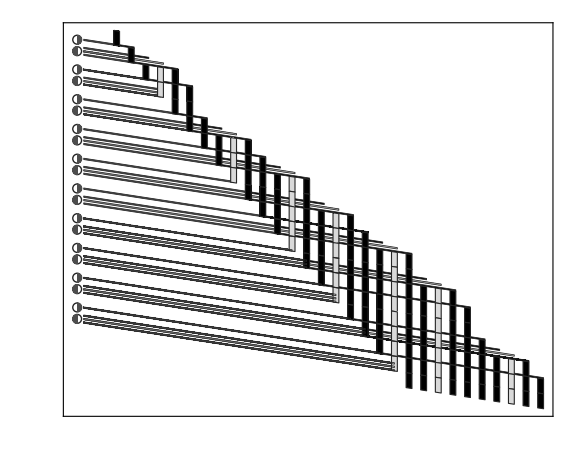

```mathematica
With[{rules=#,hist=ResourceFunction["CyclicTagSystem"][#,{1},20],icon=Function[{pos,r,phase},{GrayLevel[.15],Circle[pos,r],GrayLevel[.3],Disk[pos,r,{Pi/2,3Pi/2}+phase π]}],tk=.3,swid=.4,rht=.23},Graphics[{Table[icon[{-1.2,-i+1/2 rht (Length[rules⟦Mod[i,2,1]⟧]+.5)},.3,Mod[i,2]],{i,Length[hist]-1}],GeometricTransformation[{EdgeForm[Directive[Thickness[0.001],GrayLevel[.15]]],Table[With[{values=rules[[Mod[i,2,1]]]},{If[hist[[i,1]]==1,{GrayLevel[.85-values[[j+1]]],Polygon[{{i+.5,-i+rht j},{i+Length[hist⟦i+1⟧]-j+1-tk,-i+rht j},{i+Length[hist⟦i+1⟧]-j+1-tk,-i+rht (j+swid)},{i+.5,-i+rht(j+swid)},{i+.5,-i+rht j}}]}],GrayLevel[If[values[[j+1]]==1,.3,.6]],Polygon[{{-.75,-i+rht j},{i+.5,-i+rht j},{i+.5,-i+rht(j+swid)},{-.75,-i+rht(j+swid)},{-.75,-i+rht j}}]}],{i,Length[hist]-1},{j,0,Length[rules[[Mod[i,2,1]]]]-1}],EdgeForm[GrayLevel[.15]],MapIndexed[{GrayLevel[.85-#1],Rectangle[{First[#2]+Last[#2]-1+tk,1-First[#2]},{First[#2]+Last[#2]-tk,-First[#2]}]}&,hist,{2}]},ShearingTransform[-.15,{0,1},{1,0}]]},]]&@{{1},{1,0,1}}
```